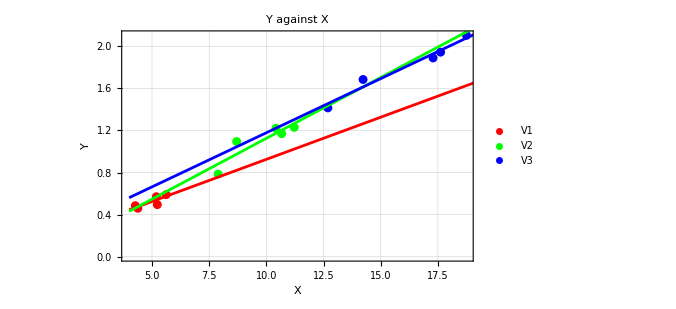

```mathematica
(*Define the data*)V1={{4.27,0.485},{5.19,0.570},{5.62,0.590},{5.23,0.495},{4.38,0.460}};
V2={{8.70,1.095},{10.42,1.220},{11.22,1.230},{10.67,1.170},{7.89,0.785}};
V3={{14.23,1.685},{17.29,1.890},{18.75,2.105},{17.62,1.945},{12.69,1.415}};

(*Extract x and y values for each set of data*)
x1=V1[[All,1]];
y1=V1[[All,2]];
x2=V2[[All,1]];
y2=V2[[All,2]];
x3=V3[[All,1]];
y3=V3[[All,2]];

(*Perform linear regression to find the best-fit lines*)
fit1=LinearModelFit[V1,x,x];
fit2=LinearModelFit[V2,x,x];
fit3=LinearModelFit[V3,x,x];

(*Plot the data points and the best-fit lines*)
Show[ListPlot[{V1,V2,V3},PlotStyle->{Red,Green,Blue},PlotLegends->{"V1","V2","V3"}],Plot[{fit1[x],fit2[x],fit3[x]},{x,4,20},PlotStyle->{Red,Green,Blue}],Frame->True,FrameLabel->{"X","Y"},GridLines->Automatic,PlotLabel->"Y against X",ImageSize->500]
```

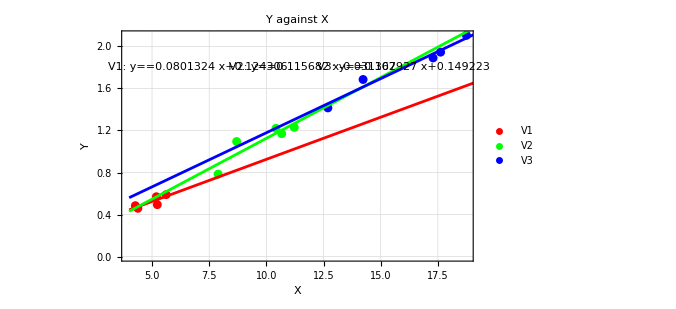

```mathematica
(*Define the data*)V1={{4.27,0.485},{5.19,0.570},{5.62,0.590},{5.23,0.495},{4.38,0.460}};
V2={{8.70,1.095},{10.42,1.220},{11.22,1.230},{10.67,1.170},{7.89,0.785}};
V3={{14.23,1.685},{17.29,1.890},{18.75,2.105},{17.62,1.945},{12.69,1.415}};

(*Extract x and y values for each set of data*)
x1=V1[[All,1]];
y1=V1[[All,2]];
x2=V2[[All,1]];
y2=V2[[All,2]];
x3=V3[[All,1]];
y3=V3[[All,2]];

(*Perform linear regression to find the best-fit lines*)
fit1=LinearModelFit[V1,x,x];
fit2=LinearModelFit[V2,x,x];
fit3=LinearModelFit[V3,x,x];

(*Plot the data points and the best-fit lines*)
Show[ListPlot[{V1,V2,V3},PlotStyle->{Red,Green,Blue},PlotLegends->{"V1","V2","V3"}],Plot[{fit1[x],fit2[x],fit3[x]},{x,4,20},PlotStyle->{Red,Green,Blue}],Frame->True,FrameLabel->{"X","Y"},GridLines->Automatic,PlotLabel->"Y against X",Epilog->{Text[Row[{"V1: ",TraditionalForm[y==fit1["BestFit"]]}],{7,1.8}],Text[Row[{"V2: ",TraditionalForm[y==fit2["BestFit"]]}],{12,1.8}],Text[Row[{"V3: ",TraditionalForm[y==fit3["BestFit"]]}],{16,1.8}]},ImageSize->500]
```

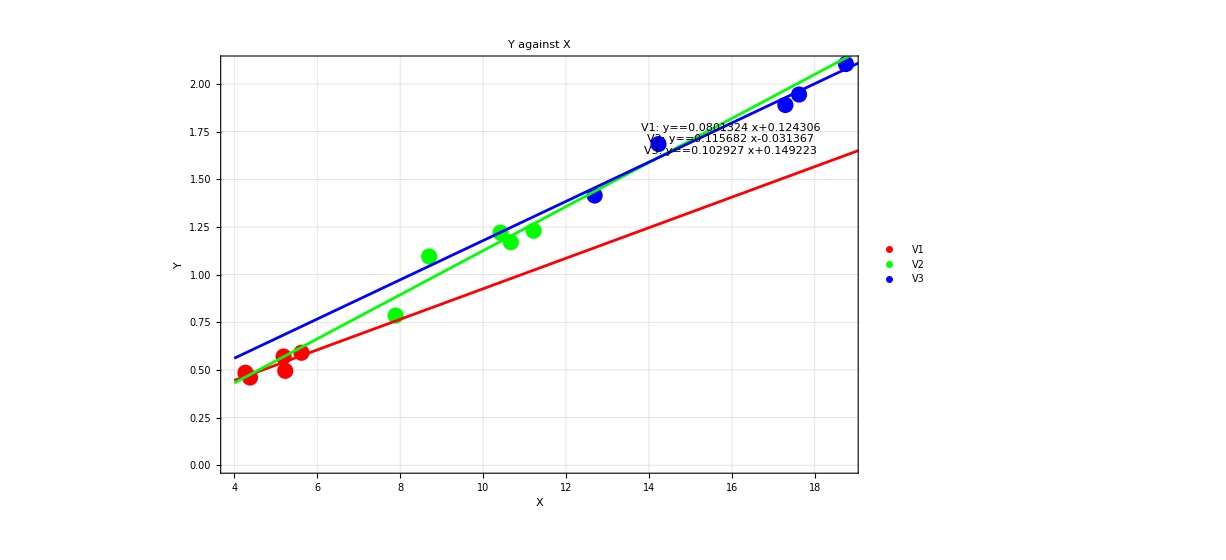

```mathematica
(*Define the data*)V1={{4.27,0.485},{5.19,0.570},{5.62,0.590},{5.23,0.495},{4.38,0.460}};
V2={{8.70,1.095},{10.42,1.220},{11.22,1.230},{10.67,1.170},{7.89,0.785}};
V3={{14.23,1.685},{17.29,1.890},{18.75,2.105},{17.62,1.945},{12.69,1.415}};

(*Extract x and y values for each set of data*)
x1=V1[[All,1]];
y1=V1[[All,2]];
x2=V2[[All,1]];
y2=V2[[All,2]];
x3=V3[[All,1]];
y3=V3[[All,2]];

(*Perform linear regression to find the best-fit lines*)
fit1=LinearModelFit[V1,x,x];
fit2=LinearModelFit[V2,x,x];
fit3=LinearModelFit[V3,x,x];

(*Display the equations outside of the graph*)
equations=Column[{Row[{"V1: ",TraditionalForm[y==fit1["BestFit"]]}],Row[{"V2: ",TraditionalForm[y==fit2["BestFit"]]}],Row[{"V3: ",TraditionalForm[y==fit3["BestFit"]]}]}];

(*Plot the data points and the best-fit lines*)
Show[ListPlot[{V1,V2,V3},PlotStyle->{Red,Green,Blue},PlotLegends->{"V1","V2","V3"}],Plot[{fit1[x],fit2[x],fit3[x]},{x,4,20},PlotStyle->{Red,Green,Blue}],Frame->True,FrameLabel->{"X","Y"},GridLines->Automatic,PlotLabel->"Y against X",Epilog->{Inset[equations,Scaled[{0.8,0.8}]]},ImageSize->500]
```

```mathematica
(*Define the data*)V1={{4.27,0.485},{5.19,0.570},{5.62,0.590},{5.23,0.495},{4.38,0.460}};
V2={{8.70,1.095},{10.42,1.220},{11.22,1.230},{10.67,1.170},{7.89,0.785}};
V3={{14.23,1.685},{17.29,1.890},{18.75,2.105},{17.62,1.945},{12.69,1.415}};

(*Extract x and y values for each set of data*)
x1=V1[[All,1]];
y1=V1[[All,2]];
x2=V2[[All,1]];
y2=V2[[All,2]];
x3=V3[[All,1]];
y3=V3[[All,2]];

(*Perform linear regression to find the best-fit lines*)
fit1=LinearModelFit[V1,x,x];
fit2=LinearModelFit[V2,x,x];
fit3=LinearModelFit[V3,x,x];

(*Plot the data points and the best-fit lines*)
plot=Show[ListPlot[{V1,V2,V3},PlotStyle->{Red,Green,Blue},PlotLegends->{"V1","V2","V3"}],Plot[{fit1[x],fit2[x],fit3[x]},{x,4,20},PlotStyle->{Red,Green,Blue}],Frame->True,FrameLabel->{"X","Y"},GridLines->Automatic,PlotLabel->"Y against X",ImageSize->500];

(*Create a column with the equations*)
equations=Column[{Row[{"V1: ",TraditionalForm[y==fit1["BestFit"]]}],Row[{"V2: ",TraditionalForm[y==fit2["BestFit"]]}],Row[{"V3: ",TraditionalForm[y==fit3["BestFit"]]}]}];

(*Display the plot and equations*)
Column[{plot,equations}]
```

-Graphics-
V1: y==0.0801324 x+0.124306
V2: y==0.115682 x-0.031367
V3: y==0.102927 x+0.149223

```mathematica
(*Define the data*)V1={{4.27,0.485},{5.19,0.570},{5.62,0.590},{5.23,0.495},{4.38,0.460}};
V2={{8.70,1.095},{10.42,1.220},{11.22,1.230},{10.67,1.170},{7.89,0.785}};
V3={{14.23,1.685},{17.29,1.890},{18.75,2.105},{17.62,1.945},{12.69,1.415}};

(*Extract x and y values for each set of data*)
x1=V1[[All,1]];
y1=V1[[All,2]];
x2=V2[[All,1]];
y2=V2[[All,2]];
x3=V3[[All,1]];
y3=V3[[All,2]];

(*Perform linear regression to find the best-fit lines*)
fit1=LinearModelFit[V1,x,x];
fit2=LinearModelFit[V2,x,x];
fit3=LinearModelFit[V3,x,x];

(*Extract equations as strings*)
eq1=ToString[TraditionalForm[y==fit1["BestFit"]]];
eq2=ToString[TraditionalForm[y==fit2["BestFit"]]];
eq3=ToString[TraditionalForm[y==fit3["BestFit"]]];

(*Display the equations outside the graph*)
Column[{Show[ListPlot[{V1,V2,V3},PlotStyle->{Red,Green,Blue},PlotLegends->{"V1","V2","V3"}],Plot[{fit1[x],fit2[x],fit3[x]},{x,4,20},PlotStyle->{Red,Green,Blue}],Frame->True,FrameLabel->{"X","Y"},GridLines->Automatic,PlotLabel->"Y against X",ImageSize->500],Column[{Row[{"V1: ",eq1}],Row[{"V2: ",eq2}],Row[{"V3: ",eq3}]}]}]
```

-Graphics-
V1: y==0.0801324 x+0.124306
V2: y==0.115682 x-0.031367
V3: y==0.102927 x+0.149223